# Path planning algorithms

## Instructions

### Execute the cells in order to obtain the results

## Initialization

### Get the Mathematica package and assign the maps to a variable

```mathematica
Get["C:\\Users\\ignam\\Dropbox\\Master Robotica\\Planificacion\\2018-ptmr\\path_planning.wl"];
maps = importMaps[];
```

## Executing the Algorithms

```mathematica
data = 
Reap[Table[
Sow[Reap[
Table[
mapX = maps[[n]][[1]];
originX = maps[[n]][[2]][[1]];
destinationX =  maps[[n]][[2]][[2]];
If[d>0,
Do[
mapX = doubleResolution[mapX];
destinationX =  destinationX *2-1;
originX = originX*2-1;
,{i, d}];
];
Sow[AbsoluteTiming[gridGraphX= buildGridGraph[mapX]; "Building grid graph"], bgg];
Sow[AbsoluteTiming[dijkstra[gridGraphX, originX-0.5, destinationX-0.5];"Dijkstra"], ggd];
Sow[AbsoluteTiming[aStar[gridGraphX, originX-0.5, destinationX-0.5];"A*"], gga];

If[d> 0, dense = 1/d, dense=1.5];
Sow[AbsoluteTiming[rrtGraphX = buildRRTGraph[mapX, originX, destinationX, dense, 2^d]; "Bulding RRT graph"], brrt];
Sow[AbsoluteTiming[dijkstraPath = dijkstra[rrtGraphX, originX-0.5, destinationX-0.5];"Dijkstra + RRT"], rrtd];
Sow[AbsoluteTiming[astarPath =aStar[rrtGraphX, originX-0.5, destinationX-0.5];"A* + RRT"], rrta];

Sow[AbsoluteTiming[TvaluesX = fastmarching[mapX, destinationX, 1]; "FM"], eik];
Sow[AbsoluteTiming[Tvalues2X = fastmarching2[mapX,destinationX, 1]; "FM2"], eik2];
Sow[AbsoluteTiming[ffPath = discreteGradientDescent[TvaluesX, originX, destinationX, 200];"Gradient Descent"], ff];



,{n, 1,Length[maps],1}]][[2]]];
,{d, {0,1,2,3,4}}]][[2]][[1]];
Export[NotebookDirectory[]<>"data.m",data]
```

ERROR: could not join the destination to the graph, try with a greater density

ERROR: could not join the destination to the graph, try with a greater density

C:\Users\ignam\Dropbox\Master Robotica\Planificacion\2018-ptmr\data.m

## Timing

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Resolution | Building Grid Graph | Dijkstra | A* | Building RRT Graph | Dijkstra+RRT | A* +RRT | Fast Marching | Fast Marching 2 | Gradient Descent
MxN | 0.191299 | 0.135045 | 0.0923392 | 22.953 | 0.334 | 0.221537 | 0.356573 | 0.721207 | 0.0081769
2Mx2N | 0.370775 | 0.551349 | 0.412657 | 23.0574 | 0.483705 | 0.356823 | 1.40967 | 3.199 | 0.0160579
4Mx4N | 1.59655 | 2.68135 | 2.67513 | 26.1185 | 0.463807 | 0.324554 | 6.39266 | 13.6106 | 0.0400023
8Mx8N | 6.93255 | 16.8066 | 24.5738 | 27.5427 | 0.805502 | 0.550266 | 28.4013 | 59.1401 | 0.0515298
16Mx16N | 33.5814 | 125.281 | 317.29 | 43.5671 | 1.65247 | 1.25035 | 131.815 | 272.93 | 0.0581842

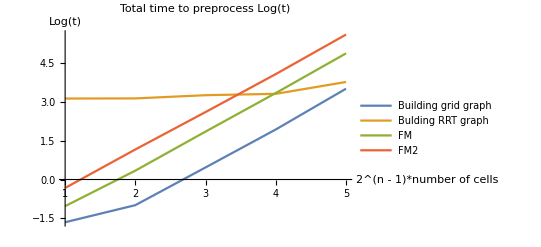

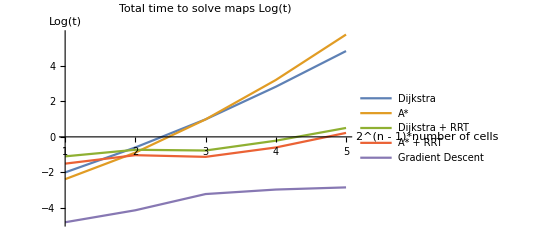

```mathematica
data = Import[NotebookDirectory[]<>$PathnameSeparator<>"data.m"];
timingdata=Map[ Total[#[[All,1]]]&,Import[NotebookDirectory[]<>$PathnameSeparator<>"data.m"], {2}];
timingdata =Transpose[Insert[Transpose[timingdata],  {"MxN","2Mx2N","4Mx4N","8Mx8N","16Mx16N"}, 1]];
images = Table[ColorNegate[Image[maps[[i,1]], ImageSize->75, ColorSpace->"Grayscale"]], {i,Length[maps]}]

TableOfValues1=Prepend[timingdata,{"Resolution","Building Grid Graph","Dijkstra","A*","Building RRT Graph","Dijkstra+RRT","A* +RRT", "Fast Marching", "Fast Marching 2", "Gradient Descent"}];

Grid[TableOfValues1,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]

preprocessplot =ListPlot[Table[Log/@Total[data[[All,i,All,1]], {2}],{i, {1,4,7,8}}], PlotLegends->data[[All, {1,4,7,8},1,2]][[1]], Joined->True, PlotLabel->Style[ "Total time to preprocess Log(t)", Black, Bold]  , AxesLabel->{"2^(n - 1)*number of cells", "Log(t)"}, AxesOrigin->{1, Automatic}]

solve =ListPlot[Table[Log/@Total[data[[All,i,All,1]], {2}],{i, {2,3,5,6,9}}], PlotLegends->data[[All, {2,3,5,6,9},1,2]][[1]], Joined->True, PlotLabel->Style[ "Total time to solve maps Log(t)", Black, Bold]  , AxesLabel->{"2^(n - 1)*number of cells", "Log(t)"}, AxesOrigin->{1, Automatic}]
```

## Animations

#### This will generate a gif for each map and for the algorithms: A*, Dijkstra and RRT

```mathematica
Do[
map = maps[[n]][[1]];
origin = maps[[n]][[2]][[1]];
destination = maps[[n]][[2]][[2]];
number = n;
graph = buildGridGraph[map];

frames =animateAstar[graph,origin-0.5, destination-0.5 ,map];
Export[NotebookDirectory[]<>"animations\\Astar\\animationAstar_map"<>ToString[number]<>"_grid"<>".gif", frames, "GIF", "DisplayDurations"->0.015];

frames =animatedijkstra[graph,origin-0.5, destination-0.5 ,map];
Export[NotebookDirectory[]<>"animations\\Dijkstra\\animationDijkstra_map"<>ToString[number]<>"_grid"<>".gif", frames, "GIF", "DisplayDurations"->0.015];

frames =animateRRT[map, origin-0.5, destination-0.5 ,1.5];
Export[NotebookDirectory[]<>"animations\\RRT\\animationRRT_map"<>ToString[number]<>".gif", frames, "GIF", "DisplayDurations"->0.015];

,{n, Length[maps]}]
```

## Images

### Select the resolution multiplicator of the image

```mathematica
Slider[Dynamic[resolution], {{1,2,3,4}}]
Dynamic[resolution]
```

### Create images for all maps

```mathematica
Do[

map= maps[[n]][[1]];
origin = maps[[n]][[2]][[1]];
destination =  maps[[n]][[2]][[2]];
If[resolution>0,
Do[
map = doubleResolution[map];
destination =  destination *2-1;
origin = origin*2-1;
,{i, resolution}];
];
Tvalues1 = fastmarching[map, destination,1];//AbsoluteTiming;
Tvalues2 = fastmarching2[map, destination,1, 4];//AbsoluteTiming;

path1 = discreteGradientDescent[Tvalues1, origin, destination, 1000];
path2 = discreteGradientDescent[Tvalues2, origin, destination, 1000];

picture1 =Map[greyToTemperature, Tvalues1/Max[Tvalues1], {2}];
picture2=picture1;

Do[picture1[[p[[1]],p[[2]]]] = {0.2,0.78,0.};,{p, path1}];
Do[picture2[[p[[1]],p[[2]]]] = {0.2,0.78,0.};,{p, path2}];

imageff = Image[picture1, ColorSpace->"RGB", ImageSize->250];
imageff2 = Image[picture2, ColorSpace->"RGB", ImageSize->250];
skeleton =showFastmarching2[map, 1];

Export[NotebookDirectory[]<>"images\\FastMarching\\fastmarching_map"<>ToString[n]<>".png", imageff, "PNG"];
Export[NotebookDirectory[]<>"images\\FastMarching\\fastmarching2_map"<>ToString[n]<>".png", imageff2, "PNG"];
Export[NotebookDirectory[]<>"images\\FastMarching\\fastmarching2_velocity_map"<>ToString[n]<>".png", skeleton, "PNG"];
,{n, Length[maps]}]
```